```mathematica
sq3=Sqrt[3];
```

```mathematica
avec={1,0};bvec={1/2,Sqrt[3]/2};
```

```mathematica
mm=5;nn=mm;
```

### Réseau nid d’abeilles

```mathematica
basis={{0,0},{0,1/sq3}};
```

```mathematica
Graphics[Line[{{1/2,-1/(2sq3)},{0,0},{0,1/sq3},{1/2,sq3/2}}]];
```

```mathematica
base={{1/2,-1/(2sq3)},{0,0},{0,1/sq3},{1/2,sq3/2}};
```

```mathematica
arr1=Table[Table[Table[basis[[l]]+i avec+j bvec,{l,Length[basis]}],{i,mm+1}],{j,0,nn+1}];arr1=Flatten[arr1,2]//N;
```

```mathematica
even=Table[arr1[[i]],{i,1,Length[arr1],2}];odd=Table[arr1[[i]],{i,2,Length[arr1],2}];
```

```mathematica
man={Line[{mm*avec+(nn+1)*bvec+base[[1]],(mm+1)*avec+(nn+1)*bvec}],Line[{base[[1]]+bvec,avec+bvec}]};
```

```mathematica
ptman={base[[1]]+bvec,(mm+1)*avec+(nn+1)*bvec};
```

```mathematica
baseHexa={{1/2,-1/(2sq3)},{0,0},{0,1/sq3},{1/2,sq3/2},{1,1/sq3},{1,0},{1/2,-1/(2sq3)}};
```

```mathematica
arrHexa=Table[Table[Line[Table[baseHexa[[l]]+i avec+j bvec,{l,Length[baseHexa]}]],{i,mm}],{j,nn}];arrHexa=Flatten[arrHexa,2]//N;
```

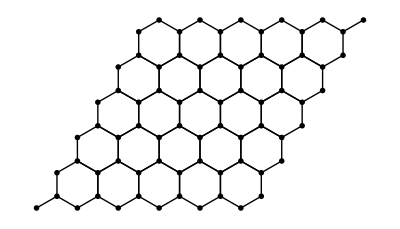

```mathematica
Graphics[{arrHexa,man},Epilog ->{PointSize[0.01], Map[Point, arr1]}]
```

### Réseau triangulaire

```mathematica
arr2=Table[Table[i avec+j bvec,{i,mm}],{j,nn}];arr2=Flatten[arr2,1]//N;
```

```mathematica
Graphics[Line[{{1,0},{0,0},{1/2,sq3/2},{1,0}}]];
```

```mathematica
baseTriangle={{1,0},{0,0},{1/2,sq3/2},{1,0}};
```

```mathematica
arrTriangle=Table[Table[Line[Table[baseTriangle[[l]]+i avec+j bvec,{l,Length[baseTriangle]}]],{i,mm}],{j,nn}];arrTriangle=Flatten[arrTriangle,2]//N;
```

#### Pas bipartite

```mathematica
Graphics[{Thick,arrTriangle,{Red,Arrowheads[0.0075],Arrow[{9avec+9bvec-{0,1/2},9avec+9bvec+{0,1/2}}]},{Red,Arrowheads[0.0075],Arrow[{9avec+10bvec+{0,1/2},9avec+10bvec-{0,1/2}}]}},Epilog ->{PointSize[0.0075], Map[Point, arr2],Text[Style["?",60,Red],10avec+9bvec]}];
```

### Spins nid d’abeilles antiferro

```mathematica
spinU[pt_]:={Red,Arrowheads[0.02],Arrow[{pt-{0,1/4},pt+{0,1/4}}]};
```

```mathematica
spinD[pt_]:={Blue,Arrowheads[0.02],Arrow[{pt+{0,1/4},pt-{0,1/4}}]};
```

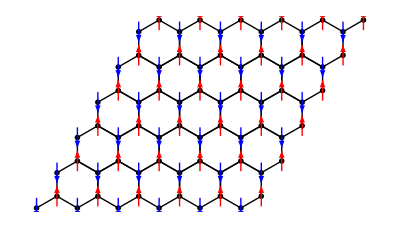

```mathematica
Graphics[{arrHexa,man},Epilog->{PointSize[0.01],Map[Point,arr1],Map[spinU[#]&,even],Map[spinD[#]&,odd]}]
```

### Réseau carré

```mathematica
baseCarre={{0,0},{1,0},{1,1},{0,1},{0,0}};
```

```mathematica
arrCarre=Table[Table[Line[Table[baseCarre[[l]]+i {1,0}+j {0,1},{l,Length[baseCarre]}]],{i,mm}],{j,nn}];arrCarre=Flatten[arrCarre,2];
```

```mathematica
arr3=Table[Table[i {1,0}+j {0,1},{i,mm+1}],{j,nn+1}];arr3=Flatten[arr3,1];
```

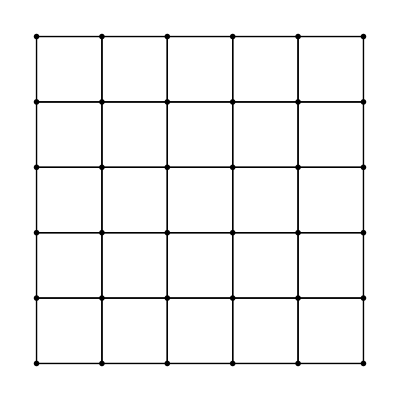

```mathematica
Graphics[arrCarre,Epilog->{{PointSize[0.01],Map[Point,arr3]}}]
```

```mathematica
Graphics[{Thick,arrCarre,{Red,Arrowheads[0.0075],Arrow[{{9,9},{10,9}}]},{Red,Arrowheads[0.0075],Arrow[{{9,9},{9,10}}]},Text[Style[a,Bold,25,Red],{9.5,8.75}],Text[Style[b,Bold,25,Red],{8.75,9.5}]},Epilog->{PointSize[0.0075],Map[Point,arr3]}];
```

### Réseau triangulaire vecteurs primitifs

```mathematica
primvect={{Red,Arrowheads[0.02],Arrow[{a*avec+b*bvec,(a+1)avec+b*bvec}]},{Red,Arrowheads[0.02],Arrow[{a*avec+b*bvec,a*avec+(b+1)bvec}]}};
```

```mathematica
textprim={Text[Style["a",Bold,15,Red],(a+1)avec+b*bvec-{1/2,1/4}],Text[Style["b",Bold,15,Red],a*avec+(b+1)bvec-{1/2,1/4}]};
```

```mathematica
ligne={Line[{(mm+1)*avec+bvec,(mm+1)*avec+(nn+1)*bvec}],Line[{(nn+1)*bvec+avec,(nn+1)bvec+(mm+1)avec}]};
```

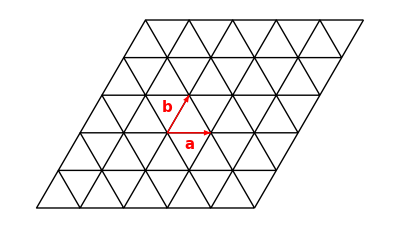

```mathematica
Graphics[{arrTriangle,primvect,ligne},Epilog->{textprim}]
```

#### Non bipartition

```mathematica
nobip={{Red,Arrowheads[0.02],Arrow[{a*avec+b*bvec-{0,1/2},a*avec+b*bvec+{0,1/2}}]},{Red,Arrowheads[0.02],Arrow[{a*avec+(b+1)bvec+{0,1/2},a*avec+(b+1)bvec-{0,1/2}}]}};
```

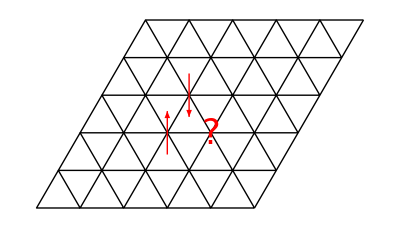

```mathematica
Graphics[{arrTriangle,nobip,ligne},Epilog ->{Text[Style["?",35,Red],(a+1)avec+b*bvec]}]
```

### Carré décoré

```mathematica
arr4=Table[Table[i {1,0}+j {0,1}+{1/2,1/2},{i,mm}],{j,nn}];arr4=Flatten[arr4,1];
```

```mathematica
Graphics[{Thick,arrCarre},Epilog->{{Red,PointSize[0.0075],Map[Point,arr3]},{Blue,PointSize[0.0075],Map[Point,arr4]}}];
```

### Triangle décoré : structure en nid d’abeilles

```mathematica
arr5=Table[Table[i avec+j bvec+avec/3+bvec/3,{i,mm}],{j,nn}];arr5=Flatten[arr5,1]//N;
```

```mathematica
Graphics[{Thick,arrTriangle},Epilog->{{Red,PointSize[0.0075],Map[Point,arr2]},{Blue,PointSize[0.0075],Map[Point,arr5]}}];
```

### Structure en nid d’abeilles : la totale

```mathematica
a=(mm+1)/2;b=(nn+1)/2;
```

```mathematica
fleche={{Arrowheads[0.02],Arrow[{a*avec+b*bvec,(a+1)avec+(b+2)bvec}]},Text[Style[Subscript[r, i],Bold,15],0.5(avec+2bvec)+a*avec+b*bvec+{0,1/4}],Text[Style[O,Bold,15],a*avec+b*bvec-{0,1/3}],Text[Style[i,Bold,15],(a+1)avec+(b+2)bvec-{0,1/3}]};
```

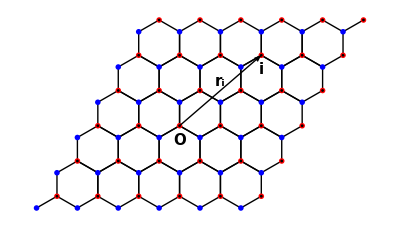

```mathematica
Graphics[{arrHexa,man},Epilog->{{Red,PointSize[0.01],Map[Point,even]},{Blue,PointSize[0.01],Map[Point,odd]},{Black,PointSize[0.005],Map[Point,even]},fleche}]
```

```mathematica
arr6=Table[Table[i avec+j bvec+base[[1]],{i,mm}],{j,nn}];arr6=Flatten[arr6,1]//N;
```

```mathematica
Graphics[{Thick,arr1,Text[Style[Subscript[r, i],Bold,25],0.5(19avec+20bvec)+{0,1/4}],Text[Style[O,Bold,25],9avec+9bvec-{0,1/3}],Text[Style[i,Bold,25],10avec+11bvec-{0,1/3}]},Epilog->{{Red,PointSize[0.0075],Map[Point,arr2]},{Blue,PointSize[0.0075],Map[Point,arr6]},{Black,PointSize[0.004],Map[Point,arr2]},{Arrowheads[0.0075],Arrow[{9avec+9bvec,10avec+11bvec}]}}];
```

### Chaîne infinie

```mathematica
chaine=Table[{i,0},{i,0,20,2}];
```

```mathematica
text={Text[Style[Subscript[x, n],Bold,15],{10,-1/2}],Text[Style[Subscript[x, n+1],Bold,15],{12,-1/2}]};
```

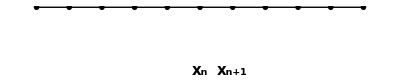

```mathematica
Graphics[{Line[{{0,0},{20,0}}],text},Epilog->{PointSize[0.01],Map[Point,chaine]}]
```

### Vecteurs delta

```mathematica
deltas={{Arrowheads[0.0075],Arrow[{9avec+9bvec,9avec+10bvec}]},{Arrowheads[0.0075],Arrow[{9avec+9bvec,10avec+9bvec}]},{Arrowheads[0.0075],Arrow[{9avec+9bvec,8avec+9bvec}]},{Arrowheads[0.0075],Arrow[{9avec+9bvec,9avec+8bvec}]},{Arrowheads[0.0075],Arrow[{9avec+9bvec,10avec+8bvec}]},{Arrowheads[0.0075],Arrow[{9avec+9bvec,8avec+10bvec}]}};
```

```mathematica
Graphics[{Thick,arr},Epilog->{{Red,PointSize[0.0075],Map[Point,arr2]},{Blue,PointSize[0.0075],Map[Point,arr6]},{Black,PointSize[0.004],Map[Point,arr2]},deltas}];
```

### Système pour calculs

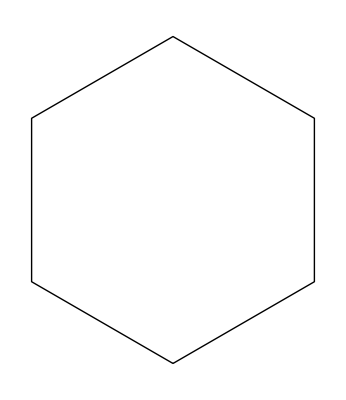

```mathematica
Graphics[Line[{{1/2,-1/(2sq3)},{0,0},{0,1/sq3},{1/2,sq3/2},{1,1/sq3},{1,0},{1/2,-1/(2sq3)}}]]
```

```mathematica
thickArrHexa=Table[Table[Line[Table[baseHexa[[l]]+i avec+j bvec,{l,Length[baseHexa]}]],{i,mm/2}],{j,nn}];thickArrHexa=Flatten[thickArrHexa,2]//N;
```

```mathematica
fleche1={Arrowheads[{-0.02,0.02}],Arrow[{bvec,(nn+1)bvec}]};
```

```mathematica
fleche2={Arrowheads[{-0.02,0.02}],Arrow[{avec,(nn+2)/2avec}]};
```

```mathematica
text12={Text[Style["L=16",15],(nn+2)/2bvec+{-1/3,1/4}],Text[Style["L/2=8",15],(nn+4)/4avec+{0,-1/2}]};
```

```mathematica
Graphics[{arrHexa,Line[{mm*avec+(nn+1)*bvec+base[[1]],(mm+1)*avec+(nn+1)*bvec}],fleche1,fleche2,text12,{Thick,thickArrHexa,Line[{base[[1]]+bvec,avec+bvec}]}}];
```

```mathematica
arrOm=Table[Table[Table[basis[[l]]+i avec+j bvec,{l,Length[basis]}],{i,(mm+1)/2}],{j,0,nn+1}];arrOm=Flatten[arrOm,2]//N;
```

```mathematica
evenOm=Table[arrOm[[i]],{i,1,Length[arrOm],2}];oddOm=Table[arrOm[[i]],{i,2,Length[arrOm],2}];
```

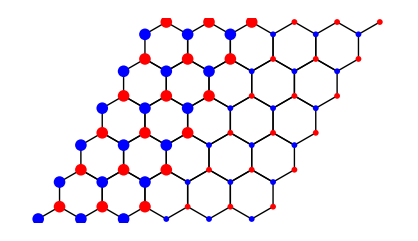

```mathematica
Graphics[{arrHexa,man},Epilog->{{PointSize[0.02],{Blue,Map[Point,oddOm]},{Red,Map[Point,evenOm]}},{PointSize[0.01],{Blue,Map[Point,odd]},{Red,Map[Point,even]}}}]
```

### Présentation

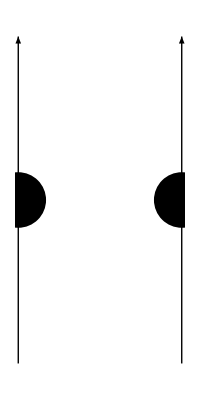

```mathematica
Graphics[{Arrowheads[0.2],Arrow[{{0,0},{0,1}}],Arrow[{{1/2,0},{1/2,1}}],PointSize[0.1],Point[{0,1/2}],Point[{1/2,1/2}]}]
```

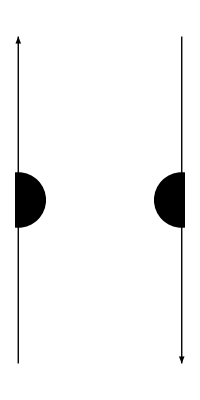

```mathematica
Graphics[{Arrowheads[0.2],Arrow[{{0,0},{0,1}}],Arrow[{{1/2,1},{1/2,0}}],PointSize[0.1],Point[{0,1/2}],Point[{1/2,1/2}]}]
```